## Parameterisation of the cone

```mathematica
(* https://math.stackexchange.com/questions/464943/parametric-equations-of-an-oblique-circular-cone *)
```

```mathematica
(* Oblique cones surface area: 
http://mathforum.org/library/drmath/view/55017.html
*)
```

```mathematica
BaseCircle:={r Cos[t], r Sin[t], 0}
```

```mathematica
Vertex:={0, d, h}
```

```mathematica
(1-ν)BaseCircle + ν Vertex
```

{r (1-ν) Cos[t],d ν+r (1-ν) Sin[t],h ν}

```mathematica
ConeAreaIntegral[r_, h_, d_]:=NIntegrate[(r √((r-d Sin[t])^2+h^2))/2,{t, 0, 2Pi}]
```

```mathematica
Integrate[(r √((r-d Sin[t])^2+h^2))/2/.d->0,{t, 0, 2Pi}]
```

π r √(h^2+r^2)

```mathematica
Solve[ r √(h^2+r^2)==rs^2, r]//FullSimplify
```

{{r→-(√(-h^2-√(h^4+4 rs^4)))/(√2)},{r→(√(-h^2-√(h^4+4 rs^4)))/(√2)},{r→-(√(-h^2+√(h^4+4 rs^4)))/(√2)},{r→(√(-h^2+√(h^4+4 rs^4)))/(√2)}}

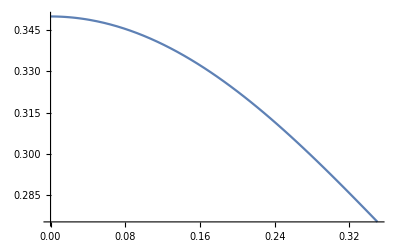

```mathematica
Plot[(√(-h^2+√(h^4+4 rs^4)))/(√2)/.rs->0.35,{h, 0, 0.35}]
```

```mathematica
ConeAreaIntegral[4, 1, 0]
```

51.8125

```mathematica
radiusWithIndentation[radiusWithoutIndentation_, indentationDepth_, offsetFromCenter_]:=r/.FindRoot[ConeAreaIntegral[r, indentationDepth, offsetFromCenter]-Pi radiusWithoutIndentation^2,{r, radiusWithoutIndentation}]//Quiet
```

```mathematica
Table[radiusWithIndentation[0.4, h, 0],{h, 0, 0.4, 0.1}]
```

{0.4,0.3938,0.375826,0.348149,0.314461}

## Simulations for Fig. 4c

```mathematica
norm[u_]:=√(u.u)

pt1:={0,((offsetFromCenter+radiusCurrent) (indentationDepth^2+(offsetFromCenter+radiusCurrent)^2-√((indentationDepth^2+(offsetFromCenter-radiusCurrent)^2) (indentationDepth^2+(offsetFromCenter+radiusCurrent)^2))))/(2 (indentationDepth^2+(offsetFromCenter+radiusCurrent)^2)),-((indentationDepth (indentationDepth^2+(offsetFromCenter+radiusCurrent)^2-√((indentationDepth^2+offsetFromCenter^2)^2+2 (indentationDepth-offsetFromCenter) (indentationDepth+offsetFromCenter) radiusCurrent^2+radiusCurrent^4)))/(2 (indentationDepth^2+(offsetFromCenter+radiusCurrent)^2)))}

pt2:={0,radiusCurrent,0}


radiusUpperBound:=norm[pt2-pt1]
immersedConeHeight:=norm[{0,offsetFromCenter,-indentationDepth}-pt1]
```

```mathematica
GiveImmersedVolume[currentOffset_]:=Module[{},
radiusInitial=0.42;
indentationDepth=0.1;
(*offsetFromCenter=0.1radiusInitial;*)
offsetFromCenter=currentOffset;
radiusCurrent=radiusWithIndentation[radiusInitial,indentationDepth, offsetFromCenter];
Pi radiusUpperBound^2 immersedConeHeight/3
]
```

```mathematica
offsetValues=Join[{10^-6//N},Table[offset,{offset,0, 0.42, 0.01}][[2;;-1]]];
list=Table[{currentOffset,GiveImmersedVolume[currentOffset]},{currentOffset,offsetValues}];
```

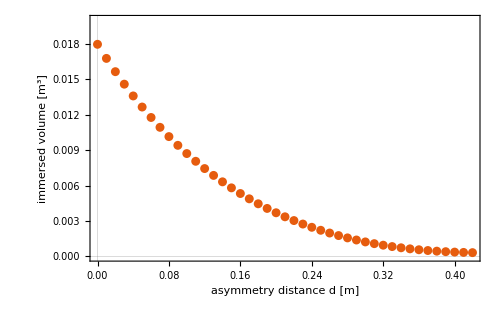

```mathematica
LP=ListPlot[list, PlotTheme->"Scientific", PlotRange->{All,{0, 0.02}}, FrameStyle->Black, ImageSize->500, BaseStyle->20, FrameLabel->{"asymmetry distance d [m]","immersed volume  [m^3]"}]
```

```mathematica
GiveImmersedPlot[currentOffset_]:=Module[{},

radiusInitial=0.42;
indentationDepth=0.1;
(*offsetFromCenter=0.1radiusInitial;*)
offsetFromCenter=currentOffset;
radiusCurrent=radiusWithIndentation[radiusInitial,indentationDepth, offsetFromCenter];

HP=Graphics3D[{Lighter@Blue, Opacity[0.5],Cuboid[pmin,pmax]}];
HP=Graphics3D[{Lighter@Blue, Opacity[0.5],InfinitePlane[{pt1, pt2,pt1+ {1, 0, 0}}]}];

PPIndented=ParametricPlot3D[{radiusCurrent (1-ν) Cos[t],offsetFromCenter ν+radiusCurrent (1-ν) Sin[t],-indentationDepth ν},{t,0,2 Pi},{ν,0,1}, PlotStyle->Directive[Green, Opacity[0.7]],PlotRange->{radiusInitial{-1,1},radiusInitial{-1,1},radiusInitial{-1,1}}, AxesLabel->{x,y, z}, PlotTheme->"Scientific", BaseStyle->20, AxesStyle->Black, ImageSize->500, BoxRatios->{1, 1, 1},  Boxed->False, Axes->False, PlotLabel->"Volume = "<>ToString[Pi radiusUpperBound^2 immersedConeHeight/3]] ;
SphereCenter=Graphics3D[{Red,  Sphere[{0,0,0},0.01]}];
e2=pt1-pt2;
e2=e2/norm[e2]; 

e3=pt1-{0,offsetFromCenter,-indentationDepth};
e3=e3/norm[e3]; 
pmax=pt1+radiusUpperBound(pt2-pt1)/norm[pt2-pt1]+radiusUpperBound{1, 0, 0};
pmin=pt1-radiusUpperBound(pt2-pt1)/norm[pt2-pt1]-radiusUpperBound{1, 0, 0}-norm[pt1-{0,offsetFromCenter,-indentationDepth}]e3;

SpherePt=Graphics3D[{Blue,  Sphere[pt1,0.01], Sphere[pmax,0.01], Sphere[pmin,0.01]}];
cylOffset=Graphics3D[{Red, Cylinder[{{0,offsetFromCenter,0},{0,offsetFromCenter,-1.1 indentationDepth}},0.005]}];
LinePlot=Graphics3D[{Tube[{pt1,pt2}],Tube[{pt1,{0,offsetFromCenter,-indentationDepth}}]}];

Show[PPIndented,(* SphereCenter, cylOffset, SpherePt,LinePlot *)HP]

]
```

```mathematica
Range[0, 0.4, 0.4/3]
```

{0.,0.133333,0.266667,0.4}

```mathematica
GiveImmersedPlot[#]&/@{10^-6, 0.13, 0.27, 0.35}
```

$Aborted

```mathematica
Pi 0.35^2
```

0.384845

```mathematica
Pi 0.42^2
```

0.554177

## Derivation of pt1 & pt2

```mathematica
$Assumptions={h>0, r>0, d>0, f∈Reals, ν>0}
norm[u_]:=√(u.u)
```

{h>0,r>0,d>0,f∈ℝ,ν>0}

```mathematica
BaseCircle:={r Cos[t], r Sin[t], 0}
```

```mathematica
Vertex:={0, d, h}
```

```mathematica
(* we consider the parameterisation *)
(1-ν)BaseCircle + ν Vertex

(* We then look at the x=0 surface, making a parametric plot in the yz plane. We also change h ν to -h ν for consistency. *)
```

{r (1-ν) Cos[t],d ν+r (1-ν) Sin[t],h ν}

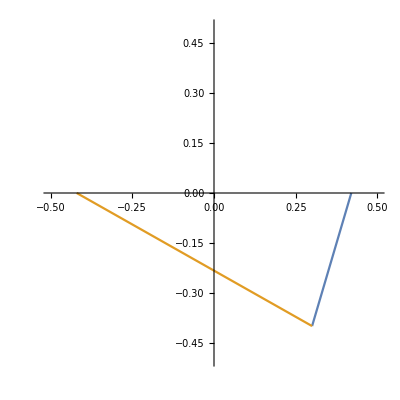

```mathematica
(* realistic parameters *)
subParams={r-> 0.42, d->0.076, h->0.1 };

(* clearer for visualisation *)
subParams={r-> 0.42, d->0.3, h->0.4 };

ParametricPlot[{{d ν+r (1-ν) Sin[t],-h ν}/.subParams/.t->Pi/2, 
{d ν+r (1-ν) Sin[t],-h ν}/.subParams/.t->Pi/2+Pi
},{ν, 0, 1}, AspectRatio->1, PlotRange->0.5{{-1,1}, {-1,1}}]
```

```mathematica
(* consider a line going from the apex at {d, -h} to {f, 0} where f is an unknown. f Will be chosen so that the line has equal angles between the orange and blue lines *)
```

```mathematica
angle1=Cos@VectorAngle[{r,0}-{d, -h},{f,0}-{d, -h}]//FullSimplify
```

(d^2+h^2+f r-d (f+r))/(√(((d-f)^2+h^2) (h^2+(d-r)^2)))

```mathematica
angle2=Cos@VectorAngle[{-r,0}-{d, -h},{f,0}-{d, -h}]//FullSimplify
```

(h^2+(d-f) (d+r))/(√(((d-f)^2+h^2) (h^2+(d+r)^2)))

```mathematica
subf=First@Solve[angle1==angle2,f]//FullSimplify
```

{f→(d^2+h^2+r^2-√(-4 d^2 r^2+(d^2+h^2+r^2)^2))/(2 d)}

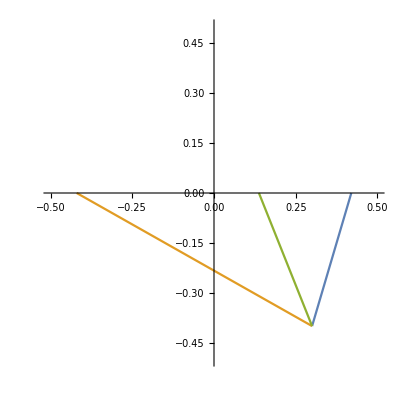

```mathematica
PP=ParametricPlot[{{d ν+r (1-ν) Sin[t],-h ν}/.subParams/.t->Pi/2, 
{d ν+r (1-ν) Sin[t],-h ν}/.subParams/.t->Pi/2+Pi, 
{f(1-ν)+d ν,-h ν}/.subf/.subParams
},{ν, 0, 1}, AspectRatio->1, PlotRange->0.5{{-1,1}, {-1,1}}]
```

```mathematica
(* We now search for a point pt1 on the green line (symmetry line emerging from apex). Now, pt1 must satisfy that apex-pt1 is orthogonal to {r, 0}-pt1. *)
```

```mathematica
online:={f(1-ν)+d ν,-h ν};
subν=Last@Solve[({r,0}-online).({d,-h}-online)==0,ν]//FullSimplify
```

{ν→-((d-f) (f-r))/((d-f)^2+h^2)}

```mathematica
(* Putting the dot product to zero, we can find the value ν on the {f(1-ν)+d ν,-h ν} line that defines pt1 *)
```

```mathematica
pt1=online/.subν/.subf//FullSimplify
```

{((d+r) (h^2+(d+r)^2-√(d^4+2 d^2 (h-r) (h+r)+(h^2+r^2)^2)))/(2 (h^2+(d+r)^2)),1/2 h (-1+(h^2+(d-r)^2)/(√(-4 d^2 r^2+(d^2+h^2+r^2)^2)))}

```mathematica
pt2={r, 0};
pt3=2 pt1-pt2;
```

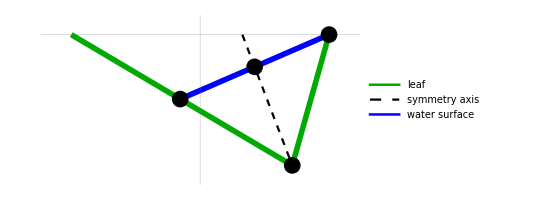

```mathematica
th=0.01;
LeafStyle=Directive[Thickness[th],Darker@Green ];
WaterStyle=Directive[Thickness[th], Blue];
AxisStyle=Directive[ Dashed, Black];

PP=ParametricPlot[{{d ν+r (1-ν) Sin[t],-h ν}/.subParams/.t->Pi/2, 
{d ν+r (1-ν) Sin[t],-h ν}/.subParams/.t->Pi/2+Pi, 
{f(1-ν)+d ν,-h ν}/.subf/.subParams,
pt2+ν( pt3-pt2)/.subParams
},{ν, 0, 1}, AspectRatio->1/2, PlotRange->0.5{{-1,1}, {-1,0}+0.1}, PlotTheme->"Scientific", PlotStyle->{LeafStyle, LeafStyle,  AxisStyle, WaterStyle}, PlotLegends->Placed[{"leaf",None, "symmetry axis", "water surface"}, {Left,Bottom}], ImageSize->400, BaseStyle->17, Frame->None];

LP=ListPlot[{pt1, pt2, pt3, {d, -h}}/.subParams, LabelStyle->15, PlotStyle->Directive[Black,PointSize[0.03]]];
PlotSlice=Show[PP, LP]
```

```mathematica
radiusUpperBound:=norm[pt2-pt1]
immersedConeHeight:=norm[{d,-h}-pt1]
```

```mathematica
(* points in 3D *)
```

```mathematica
P1=Join[{0}, pt1];
P2=Join[{0}, pt2];
P3=Join[{0}, pt3];
PApex={0, d, -h};
```

```mathematica
LeafStyle=Directive[Thickness[th],Darker@Darker@Green ];

PPLines=ParametricPlot3D[{{0, d ν+r (1-ν) Sin[t],-h ν}/.subParams/.t->Pi/2, 
{0, d ν+r (1-ν) Sin[t],-h ν}/.subParams/.t->Pi/2+Pi, 
{0, f(1-ν)+d ν,-h ν}/.subf/.subParams,
P2+ν( P3-P2)/.subParams
},{ν, 0, 1}, AspectRatio->1, PlotRange->0.5{{-1,1}, {-1,1}},PlotStyle->{LeafStyle, LeafStyle,  AxisStyle, WaterStyle}];

range=r/.subParams;
PP=ParametricPlot3D[{r (1-ν) Cos[t],d ν+r (1-ν) Sin[t],-h ν}/.subParams,{t,0,2 Pi},{ν,0,1}, PlotStyle->Directive[Green, Opacity[0.6]],AxesLabel->{x,y, z}, PlotTheme->"Scientific", BaseStyle->20, AxesStyle->Black, ImageSize->500, BoxRatios->{1, 1, 1},  Boxed->False, Axes->False,PlotRange->range{{-1,1},{-1,1},{-1,1}}];

HP=Graphics3D[{Lighter@Blue, Opacity[0.5],InfinitePlane[{P1, P2,P1+ {1, 0, 0}}/.subParams]}];
HP2=Graphics3D[{Lighter@Orange, Opacity[0.7],InfinitePlane[{P1, P2, {0, 0, 0}}/.subParams]}];

PlotFull=Show[PP,PPLines, HP]
```

-Graphics3D-

```mathematica
Grid[{{PlotFull},{ PlotSlice}}]
```

-Graphics3D- | -Graphics-

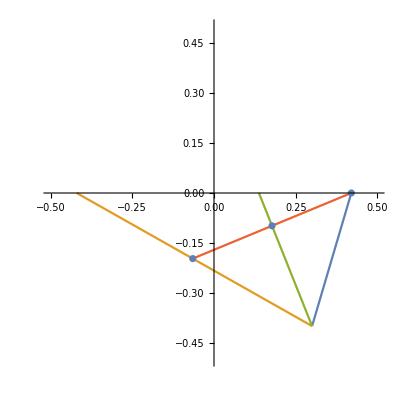

```mathematica
SP
```

## Sliced geometry

```mathematica
P1=Join[{0}, pt1];
P2=Join[{0}, pt2];
P3=Join[{0}, pt3];
PApex={0, d, -h};
```

```mathematica
PR[r_, h_, d_]:=ParametricRegion[{{ρ(1-ν) Cos[t],d ν+ρ (1-ν) Sin[t],-h ν},ν<0.5||ν>0.5},{{t,0,2 π},{ν, 0, 1}, {ρ, 0,r }}]
```

```mathematica
PR[r, h, d]/.subParams//DiscretizeRegion
```

-Graphics3D-

```mathematica
GiveImmersedVolumeDiscrete[rinput_, hinput_, dinput_]:=Module[{area},
r=rinput; h=hinput; d=dinput;
MR=PR[r, h, d]//Evaluate//DiscretizeRegion;
f={x,y,z}↦({x, y, z}-P1).(P1-PApex)//Evaluate;
plot=SliceContourPlot3D[1,f[x,y,z]==0,{x,y,z}∈MR];
DG3=DiscretizeGraphics[plot];
area=Area[DG3] immersedConeHeight/3;
Clear[r,h,d];
area

]
```

```mathematica
discreteVolumes=Table[GiveImmersedVolumeDiscrete[0.42,0.1,d],{d, 0, 0.4, 0.1/2}]
```

DiscretizeRegion::bdprbnds: The bounds associated with the ParametricRegion variables are not a list of {min, max} pairs.

SliceContourPlot3D::idomdim: {x,y,z}∈MR does not have a valid dimension as a plotting domain.

$Assumptions::fas: Warning: one or more assumptions evaluated to False.

Area::reg: DiscretizeGraphics[SliceContourPlot3D[1,f[x,y,z]==0,{x,y,z}∈MR]] is not a correctly specified region.

{0.00110132,0.0129447,0.00913932,0.00636201,0.00431719,0.00282364,0.00178248,0.00110263,0.00076341}

```mathematica
dvalues=Table[d, {d, 0, 0.4, 0.1/2}]
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4}

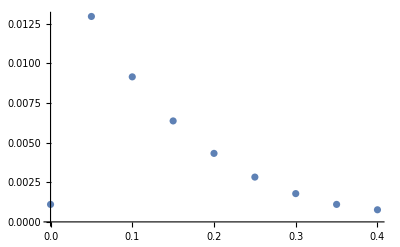

```mathematica
LP2=ListPlot[Transpose@{dvalues, discreteVolumes}, PlotRange->All]
```

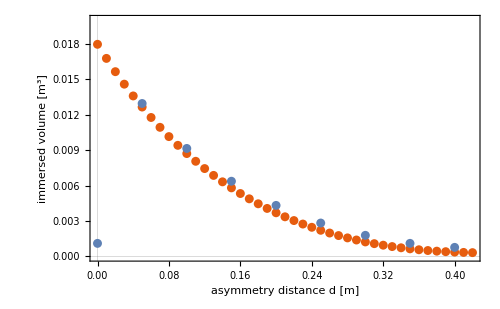

```mathematica
Show[LP, LP2]
```